# 2D Meshes and Shape Functions on the Reference Triangle

A 2D triangular mesh is just a bunch of labeled triangles with labels on the vertices (corners)  and edges (lines) tied together with some data structure that connects
	triangles⟷edges⟷points⟷triangles.
I am trying to say that you can ask for the points associated with any triangle, the triangles associated with any point, the lines associated with any triangle, the triangles associated with any line, etc.

### Reference Triangle

Every triangle is just a squashed version of the reference triangle defined by P_1={0,0},P_2={1,0}, and P_3={0,1}

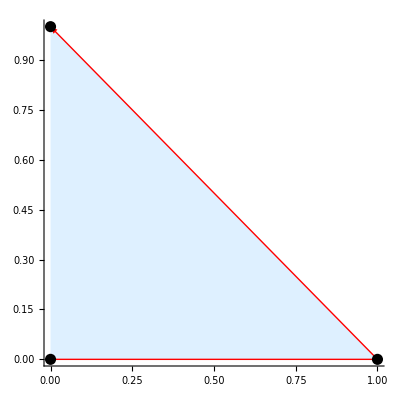

```mathematica
Ps={{0,0},{1,0},{0,1}};
Graphics[{
{LightBlue,Polygon[Ps]},
{Red, Thick, Arrow[Ps]},
{Black, PointSize[0.02], Point[Ps]}},Axes->True]
```

### Reference Linear Shape Functions

On the reference triangle Ps={{0,0},{1,0},{0,1}} we have simple nodal linear functions 1-(X+Y), X,Y

```mathematica
Plot3D[ {1-(X+Y),X,Y},{X,0,1},{Y,0,1-X},
PlotLegends->Automatic,
PlotLabel->"Basic Linear Shape Functions"
]
```

-Graphics3D-

I can build a linear function that interpolates three nodal values (z values at P_1, P_2, and P_3)  just by multiplying the appropriate functions by the values and adding them together. In other words, 
	z_1 F_1(X,Y)+z_2 F_2(X,Y)+z_3 F_3(X,Y)=z_1(1-X-Y) + z_2 X+ z_3 Y
interpolates the values at the corners.  A picture is worth a thousand words!

```mathematica
{z1,z2,z3}={1.2,-3.4,2.1};
Show[
Plot3D[ z1(1-X-Y) + z2 X+ z3 Y,{X,0,1},{Y,0,1-X},
PlotLabel->"Linear Interpolation"
],
Graphics3D[{Red, PointSize[0.03],Point[{{0,0,z1},{1,0,z2},{0,1,z3}}]}]
]
```

-Graphics3D-

### Reference Triangle Transformation

Since every triangle is just a squashed version of the reference triangle defined by P_1={0,0},P_2={1,0}, and P_3={0,1}. I can map any triangle say
	{p_1,p_2,p_3} 
to the reference triangle. It is easiest to think about going the other way from the reference triangle to {p_1,p_2,p_3} !  In fact,
	p_1 F_1(X,Y)+p_2 F_2(X,Y)+p_3 F_3(X,Y)=p_1(1-X-Y) + p_2 X+ p_3 Y
is clearly the transformation we want!

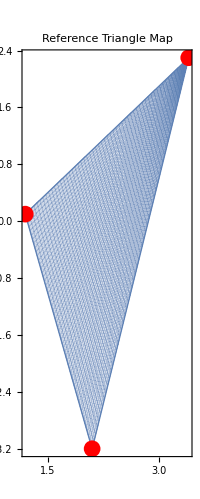

```mathematica
{p1,p2,p3}={{1.2,0.1},{3.4,2.3},{2.1,-3.2}};
Show[
ParametricPlot[ p1(1-X-Y) + p2 X+ p3 Y,{X,0,1},{Y,0,1-X},
PlotLabel->"Reference Triangle Map"
],
Graphics[{Red, PointSize[0.03],Point[{p1,p2,p3}]}]
]
```

### Reference Triangle Reverse Transformation

The map
	(X,Y)->p_1(1-X-Y) + p_2 X+ p_3 Y
takes the reference triangle to the triangle defined by the points {p1,p2,p3}.  If we invert it we will get a map 
	(x,y)-> (X(x,y),Y(x,y))
from triangle {p1,p2,p3} to the reference triangle. Clearly the recipe depends on the vertices {p1,p2,p3} and is not going to be that pretty!

Write p1={x1,y1}, p2={x2,y2}, and p3={x3,y3}.  The I need to solve the two equations 
	x_1(1-X-Y) | + | x_2 X | + | x_3 Y | = | x
y_1(1-X-Y) | + | y_2 X | + | y_3 Y | = | y
for X and Y. Two linear equations in these two unknowns so I am good! Rearrange a bit to get 
	(x_2-x_1)X | + | (x_3-x_1)Y | = | x-x_1
(y_2-y_1)X | + | (y_3-y_1)Y | = | y-y_1
which gives 
	(X
Y)=(x_2-x_1 | x_3-x_1
y_2-y_1 | y_3-y_1)^-1(x-x_1
y-y_1)
you can compute the inverse if you want!  The problem here is knowing which (x,y) you can plug in! In other words which ones are inside your triangle!  Almost all computations are done in the reference configuration.  Note the matrix for any triangle is constant!

### Fancy Shape Functions on Triangles

On the reference triangle Ps={{0,0},{1,0},{0,1}}  I can add mid point nodes
	{{0.5,0},{0.5,0.5},{0,0.5}}

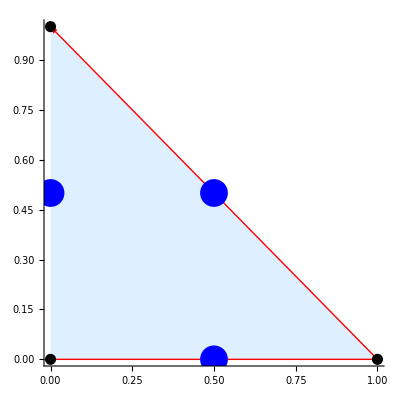

```mathematica
Ps={{0,0},{1,0},{0,1}};
NewPs = {{0.5,0},{0.5,0.5},{0,0.5}};
Graphics[{
{LightBlue,Polygon[Ps]},
{Red, Thick, Arrow[Ps]},
{Black, PointSize[0.02], Point[Ps]},
{Blue, PointSize[0.05], Point[NewPs]}
},
Axes->True]
```

and make fancier nodal quadratic shape functions  (called P_2) as follows 
	2X(X-1/2), 2Y(Y-1/2), etc. 
The real questions are

How many quadratics should there be?

The answer is 6 since quadratics are sums of  1, X, Y, X*Y, X^2, Y^2.

The fancy way of saying this is the quadratics are in the span of these functions.  The functions are linearly independent.  So the dimension of the quadratics in 2D is 6.

What should we use as a basis and should we number the basis?

We want a nodal basis: six functions that are zero at all dots except one

We should number them the same way we number the six points on the reference triangle.

We are going to do this by hand and then think about how to automate it!

```mathematica
P2Fns = {(1-(X+Y))* (1-2(X+Y)), X(2X-1),Y(2 Y-1),4X(1-(X+Y)),4 X Y,4Y(1-(X+Y))};
Show[
Plot3D[ P2Fns,{X,0,1},{Y,0,1-X},
PlotLegends->P2Fns,
PlotStyle->Opacity[0.5],
PlotRange->All,
PlotLabel->"Quadratic Shape Functions"
],
Graphics3D[{
{Red, PointSize[0.03],Point[ {{0,0,0},{1/2,0,0},{1,0,0},{1/2,1/2,0},{0,1,0},{0,1/2,0}}]},
{Cyan, PointSize[0.03],Point[ {{0,0,1},{1/2,0,1},{1,0,1},{1/2,1/2,1},{0,1,1},{0,1/2,1}}]}
}]
]
```

-Graphics3D-

I can build a quadratic function that interpolates six nodal values (z values at P_1→P_6)  just by multiplying the appropriate functions by the values and adding them together. In other words, 
	Q[{X_,Y_}] = ∑_(i=1)^6 z_i *F_i[{X,Y}]
interpolates the values at the corners and mid points.

```mathematica
Clear[f,X,Y]
f[{X_,Y_}]:= Cos[ 3X+2 Y^2+Exp[4X Y]]+1.2 X
P1s={{0,0},{1,0},{0,1}};
P2s=Join[P1s,{{0,0.5},{0.5,0.5},{0.5,0}}];
F1s ={1-(X+Y),X,Y};
F2s = {(1-(X+Y))*(1-2(X+Y)),X(2X-1),Y(2 Y-1), 4Y*(1-(X+Y)),4X*Y,4X*(1-(X+Y))};
LinInterp[{X_,Y_}]=Sum[ f[P1s[[i]]]*F1s[[i]],{i,1,3}];
QInterp[{X_,Y_}]=Sum[ f[P2s[[i]]]*F2s[[i]],{i,1,6}]
Show[
Plot3D[ f[{X,Y}], {X,-0.1,1.1},{Y,-0.1,1.1-X},PlotStyle->Opacity[0.5]],
Plot3D[LinInterp[{X,Y}],{X,0,1},{Y,0,1-X},
PlotStyle->Blue
],
Plot3D[QInterp[{X,Y}],{X,0,1},{Y,0,1-X},
PlotStyle->Orange
],
Graphics3D[{PointSize[0.05],
{Green, Table[{XX,YY}=P2s⟦i⟧;Point[{XX,YY,f[{XX,YY}]}],{i,Length[P2s]}]}
}
]
]
```

0.546356 X (-1+2 X)-0.804574 X (1-X-Y)+2.42357 X Y+0.282949 (1-X-Y) Y-0.989992 Y (-1+2 Y)+0.540302 (1-X-Y) (1-2 (X+Y))

-Graphics3D-

# 2D Meshes and Single Point (Node) Shape Functions

Each point in a mesh is on several triangles!  I am going to pick a point and draw the “tent” function associated with that point. There are several steps:
1) Find the triangles that contain the chosen point.
2) Make the linear function on each of these triangles that is 1 at the chosen point and zero at the other two vertices. 
3) Plot and admire the “tent” function.

Before we build a function I need to work out how to do it!

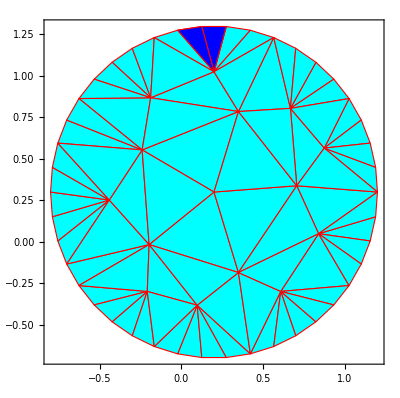

-Graphics3D-

```mathematica
ChosenPoint = 12;
Omega = DiscretizeRegion[Disk[{0.2,0.3},1],
MaxCellMeasure->{"Area"->0.2},
MeshCellLabel->{0->"Index"},
MeshCellHighlight->{{0,ChosenPoint}->Directive[Red,PointSize[0.03]]}
];
Points=MeshCoordinates[Omega];
VPoints=Points/.{x_,y_}->{x,y,0}; VPoints⟦ChosenPoint,3⟧=1;
Polys= MeshCells[Omega,{2}];Indices = Position[Polys⟦All,1⟧,ChosenPoint]⟦All,1⟧;
Graphics[GraphicsComplex[Points,{EdgeForm[Red],
{Cyan, Polys},
{Blue,Polys[[Indices]]}
}],
Frame->True]
Graphics3D[GraphicsComplex[VPoints,{EdgeForm[Red],
{Cyan, Polys},
{Blue,Polys[[Indices]]}
}],
Boxed->True,
Axes->True]
```

## Piecewise Linear Interpolation

The tepee functions are piecewise linear!
-Graphics-

They are zero off their multi-triangle base!  They are zero all round the edge of their polygonal base! They are unit height at the central peak!

All I have to do to interpolate data is multiply the appropriate function value with the appropriate tent function and I get a piecewise linear function interpolating (fancy word for matching) a given function. This is shockingly easy to visualize

```mathematica
f[{x_,y_}]:= Sin[x + Cos[x ArcTan[x/(x^2+y^2)+ Sin[y]]+ Sin[x y^2]]]
VPoints=Points/.{x_,y_}->{x,y,f[{x,y}]};
Polys= MeshCells[Omega,{2}];
Show[Plot3D[ f[{x,y}],{x,y}∈Omega],
Graphics3D[GraphicsComplex[VPoints,Polys]]]
Graphics3D[GraphicsComplex[VPoints,Polys],
Axes->True]
```

-Graphics3D-

-Graphics3D-

Smaller triangles better picture!

```mathematica
Omega = DiscretizeRegion[Disk[{0.2,0.3},1],
MaxCellMeasure->{"Area"->0.0025},
MeshCellLabel->{0->"Index"},
MeshCellHighlight->{{0,ChosenPoint}->Directive[Red,PointSize[0.03]]}
];
Points=MeshCoordinates[Omega];
Polys= MeshCells[Omega,{2}];
VPoints=Points/.{x_,y_}->{x,y,f[{x,y}]};
Graphics3D[GraphicsComplex[VPoints,Polys],
Axes->True,
PlotLabel->StringForm["`` points & `` Δ", Length[Points],Length[Polys]]]
```

-Graphics3D-

## Piecewise Linear Interpolation: Quality

How should we measure the “quality” of a piecewise linear interpolation? 
How should we measure the “quality” of a mesh?
How does the quality of the piecewise linear interpolation depend on the quality of the mesh?

When solving a PDE we do not know the function we are approximating.  It is the solution of the PDE.

The strength of Finite Elements is that it gives us the "best" linear interpolation to the solution of our PDE.  This optimality property gives a lot of usefull properties.